```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
Coords = Import["CrossHoleSymData/Coordinates.JSON", "RawJSON"];
Elements = Import["CrossHoleSymData/elements.txt","Table","FieldSeparators"->","];
Elements = Drop[Elements, None, {1}];
UndeformedCoords = Table[{},{i,1,Length[Keys[Coords]]}];
DeformedCoords = Table[{},{i,1,Length[Keys[Coords]]}];
For[i=1, i<=Length[Keys[Coords]], i++,
UndeformedCoords[[i]] = Coords[ToString[i]]["undeformed"];
DeformedCoords[[i]] = Coords[ToString[i]]["deformed"];
];
Nodes = UndeformedCoords;
```

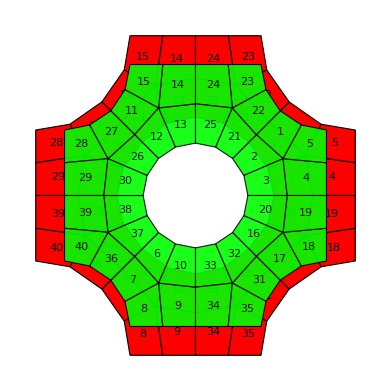

```mathematica
(*Izris deformacij*)
 ELplot= Table[{
	Graphics[{Opacity[0.9],
Green,EdgeForm[Black],Polygon[UndeformedCoords[[Elements[[i]]]]],Black,Text[ToString[i],Mean[UndeformedCoords[[Elements[[i]]]]]]
}]},
	{i,1,Length[Elements]}];

ELplot2= Table[{
	Graphics[{
Red,EdgeForm[Black],Polygon[DeformedCoords[[Elements[[i]]]]],Black,Text[ToString[i],Mean[DeformedCoords[[Elements[[i]]]]]]
}]},
	{i,1,Length[Elements]}];

Show[ ELplot2,ELplot]
```

```mathematica
(*Sile in pomiki*)
```

```mathematica
Force1 = Import["CrossHoleSymData/RF1.txt", "Table", HeaderLines -> 4][[1;;-5,2]];
Force2 = Import["CrossHoleSymData/RF2.txt", "Table", HeaderLines -> 4][[1;;-5,2]];
U1 = Import["CrossHoleSymData/U1.txt", "Table", HeaderLines -> 4][[1;;-5, 2]];
U2 = Import["CrossHoleSymData/U2.txt", "Table", HeaderLines -> 4][[1;;-5, 2]];
ALLWK = Import["CrossHoleSymData/ALLWK.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];
t = Import["CrossHoleSymData/U1.txt", "Table", HeaderLines -> 4][[1;;-5, 1]];
NumericnaIntegracija[X_, Y_ ] := Module[{I = 0* X},
ls = Length[Y];
(*Print[δW];*)
For[i = 1, i < ls, i++,
		I[[i+ 1]] = I[[i]] + (Y[[i+1]]  + Y[[i]])/2 * (X[[i+1]] - X[[i]]);
	];
Return[I];
];
```

```mathematica
δW1 = 2 * NumericnaIntegracija[U1, Force1];(*2 -> saj je sila v obe smeri*)
δW2 = 2 * NumericnaIntegracija[U2, Force2];
δWsk = δW1 + δW2;
```

```mathematica
P1  =ListLinePlot[δW1, AxesOrigin->{1,0}, PlotLegends->{"δW1"}, PlotStyle->{Green}];
P2  =ListLinePlot[δW2, AxesOrigin->{1,0}, PlotLegends->{"δW2 "}, PlotStyle->{Blue,Dashed}];
Pawk = ListLinePlot[ALLWK, AxesOrigin->{1,0}, PlotLegends->{"δALLWK "}, PlotStyle->{Green,Dashed}];
Psk  =ListLinePlot[δWsk, AxesOrigin->{1,0}, PlotLegends->{"δWsk - skupno delo"}, PlotStyle->Red];
```

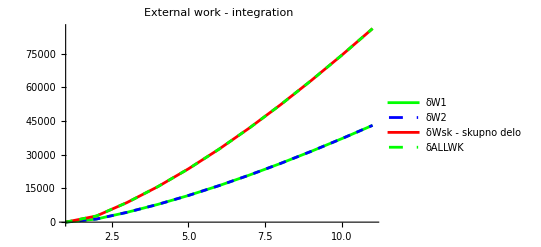

```mathematica
Show[P1, P2, Psk,Pawk, PlotRange -> All, PlotLabel -> "External work - integration"]
```

### Notranje delo

```mathematica
F = Import["CrossHoleSymData/Grad_PHANTOM.JSON", "RawJSON"];
NAP = Import["CrossHoleSymData/Stress.JSON", "RawJSON"];

Frames = Length[Keys[F]] -1;
nelements = Length[Keys[F["1"]]];
ngp = Length[Keys[F["1"][["1"]]]];
determinants = Table[{},{i,1,nelements}];
d = 0.8; (*mat. thick*)

{Keys[F], Keys[NAP]} // MatrixForm
```

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10)

```mathematica
Wint = Table[0,{i,1, Frames +1}];
WintL = Table[0,{i,1, Frames +1}]; (*L -> Using the definition for P.K*)
For[frame=1, frame <= Frames, frame++,
Print["frame: ",frame];

ΔWint = 0;
For[element=1, element <= nelements, element++,
	(*Determinant*)
	det = {};
	Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
	Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
	Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
	Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
	Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);
	x = Nodes[[Elements[[element]]]][[;;,1]];
	y = Nodes[[Elements[[element]]]][[;;,2]];
	
	X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
	Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
	J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});
	
	det = 
	{Det[J[-1/(√3),-1/(√3)]],
	Det[J[1/(√3),-1/(√3)]],
	Det[J[-1/(√3),1/(√3)]],
	Det[J[1/(√3),1/(√3)]]} ;

	Wele= 0;
	For[gp=1, gp <= ngp, gp++,
		(*Gradient in odvod gradienta*)
		Fcf = F[ToString[frame]][ToString[element]][ToString[gp]][["F"]]; (*gp -> Current gauss integration point*)
		Fpf = F[ToString[frame-1]][ToString[element]][ToString[gp]][["F"]]; (*pf -> Previous frame*)
		{F11cf, F12cf, F21cf, F22cf, F33cf} = {Fcf[[1]],Fcf[[2]],Fcf[[3]],Fcf[[4]],Fcf[[5]]};
 (*Current frame*)

		{F11pf, F12pf, F21pf, F22pf, F33pf} = {Fpf[[1]],Fpf[[2]],Fpf[[3]],Fpf[[4]],Fpf[[5]]}; (*Previous frame*)
		
		(*Odvod!*)
		{δF11, δF12, δF21, δF22, δF33} = (Fcf - Fpf);
		(*
		Tu ne racunamo L, ampak samo Ḟ, saj smo inverz ze uporabili v izracunu enacb
		*)
		
		(*Napetosti*)
		σcf = NAP[ToString[frame]][ToString[element]][ToString[gp]][["S"]]; (*cf -> current frame*)
		σpf = NAP[ToString[frame-1]][ToString[element]][ToString[gp]][["S"]]; (*fp -> previous frame*)

		{σ11cf, σ12cf, σ22cf} = {σcf[[1]],σcf[[4]],σcf[[2]]};
		{σ11pf, σ12pf, σ22pf} = {σpf[[1]],σpf[[4]],σpf[[2]]};


		(*1st Piola-Kirchoff stress  P*)
		(*current frame -> cf*)
		p11cf=F33cf (F22cf σ11cf-F12cf σ12cf);
		p12cf=-F21cf F33cf σ11cf+F11cf F33cf σ12cf;
		p21cf=F33cf (F22cf σ12cf-F12cf σ22cf);
		p22cf=-F21cf F33cf σ12cf+F11cf F33cf σ22cf;

		(*previous frame*)
		p11pf=F33pf (F22pf σ11pf-F12pf σ12pf);
		p12pf=-F21pf F33pf  σ11pf+F11pf F33pf σ12pf;
		p21pf=F33pf (F22pf σ12pf-F12pf σ22pf);
		p22pf=-F21pf F33pf σ12pf+F11pf F33pf σ22pf;

		(*Average 1.st PK*)
		p11 = (p11cf + p11pf)/2;
		p12 = (p12cf + p12pf)/2;
		p21 = (p21cf + p21pf)/2;
		p22 = (p22cf + p22pf)/2;
		
		Wele += d *  det[[gp]]*(p11 δF11 + p12 δF12 + p21 δF21 + p22 δF22);

];(*Gauss Integration Point*)
ΔWint += Wele;

];(*Elements*)
Wint[[frame+1]] = Wint[[frame]] + ΔWint;

];(*Frame*)
```

frame: 1

frame: 2

frame: 3

frame: 4

frame: 5

frame: 6

frame: 7

frame: 8

frame: 9

frame: 10

### Izris

{0.,136.398,709.582,1935.43,3911.92,6726.5,10457.7,15175.9,20944.6,27820.4,35854.1}

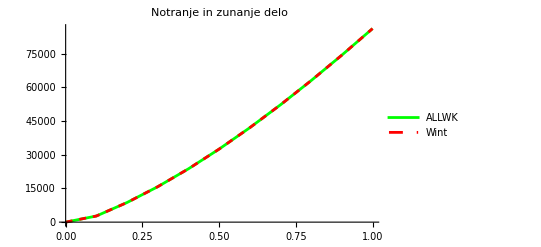

```mathematica
Wint2= NumericnaIntegracija[t,Wint]
P1 = ListLinePlot[{t,ALLWK}ᵀ, PlotLegends-> {"ALLWK"}, PlotStyle->{Green}];
P2 = ListLinePlot[{t,Wint}ᵀ, PlotLegends-> {"Wint"}, PlotStyle->{Red,Dashed}];

Show[P1, P2, PlotRange->All, PlotLabel -> "Notranje in zunanje delo"]
```

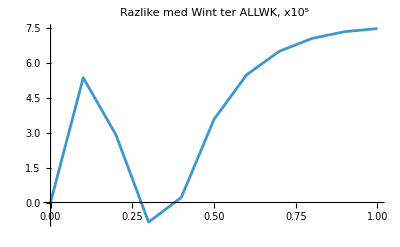

```mathematica
ListLinePlot[{t, (1 - (Wint+10^-12)/(ALLWK+10^-12))*10^5}ᵀ, PlotLabel->"Razlike med Wint ter ALLWK, x10^5"]
```